```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/sid/Academics/Case Western Reserve University/Semester 4/Quantum Computers/Project/Graphs

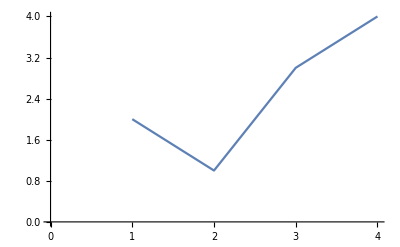

```mathematica
ListLinePlot[{2,1,3,4}]
```

```mathematica
f[x_]=x^4-3 x^2+x
```

x-3 x^2+x^4

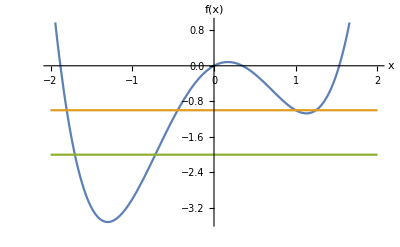

Function.jpg

```mathematica
Plot[{f[x],-1,-2},{x,-2,2},AxesLabel->{"x","f(x)"}]
Export["Function.jpg",%]
```

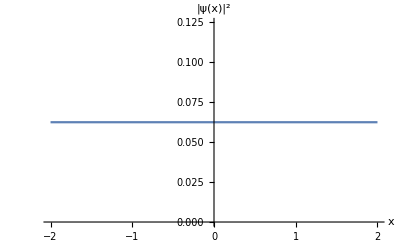

Init.jpg

```mathematica
Plot[1/16,{x,-2,2},AxesLabel->{"x","|ψ(x)|^2"}]
Export["Init.jpg",%]
```

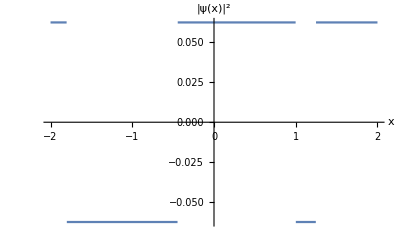

Oracle1.jpg

```mathematica
Plot[1/16 Sign[f[x]-(-1)],{x,-2,2},AxesLabel->{"x","|ψ(x)|^2"}]
Export["Oracle1.jpg",%]
```

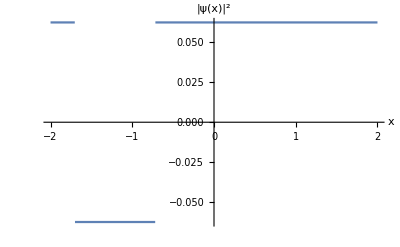

Oracle2.jpg

```mathematica
Plot[1/16 Sign[f[x]-(-2)],{x,-2,2},AxesLabel->{"x","|ψ(x)|^2"}]
Export["Oracle2.jpg",%]
```